# Analizador de datos

## Inicialización

```mathematica
(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 400;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

```mathematica
path = FileNameJoin[{$HomeDirectory,"HuertosLog"}];
SetDirectory[path];
```

## Contadores de experimentos y rondas

```mathematica
GetNumberOfExperiments[]:=Module[{x},
Max[Map[First[StringCases[#,"Experimento_"~~x_~~_:>ToExpression[x]]]&,FileNames[]]]
];
GetNumberOfRounds[experiment_]:=Module[{expString,rounds,x},
expString = "Experimento_"<>ToString[experiment]<>"_Ronda_";
rounds = Flatten[Map[StringCases[#,expString~~x__:>ToExpression[x]]&,FileNames[]]];
Max[rounds]
];
GetNumberOfFruits[experiment_,round_,player_]:=Module[{pathStr,filesInPath,pattExpr,fruits},
pathStr = "Experimento_"<>ToString[experiment]<>"_Ronda_"<>ToString[round];
filesInPath = Map[FileBaseName,FileNames[All,pathStr]];
pattExpr = "fruit_"<>player<>"_";
fruits = DeleteCases[Map[StringCases[#,pattExpr~~x__:>ToExpression[x]]&,filesInPath],{}];
Max[Flatten[fruits]]
];
```

```mathematica
GetNumberOfFruits[1,1,"PlayerB"]
```

50

```mathematica
GetNumberOfRounds[1]
```

3

```mathematica
GetNumberOfExperiments[]
```

6

## Graficador de ruta de cursores

```mathematica
PositionParse[position_String]:=Map[ToExpression,StringSplit[StringTake[position,{2,-2}],","]];
GetCursorData[experiment_,round_,cursor_]:=Block[{path,rawData,dated,numericPosition,formatted},
path = "Experimento_"<>ToString[experiment]<>"_Ronda_"<>ToString[round];
rawData = Drop[Import[FileNameJoin[{path,"cursordata_"<>cursor<>".csv"}]],1];
dated = MapAt[DateObject,rawData,{All,1}];
numericPosition = MapAt[PositionParse,dated,{All,2}];
formatted = Map[Association[Thread[{"Date","Position","Selecting","Access"}->#]]&,numericPosition];
Dataset[formatted]
];
PlotCursorPaths[experiment_,round_]:=Block[{cursorAPos,cursorBPos},
cursorAPos = Normal[GetCursorData[experiment,round,"CursorA"][All,"Position"]];
cursorBPos = Normal[GetCursorData[experiment,round,"CursorB"][All,"Position"]];
ListLinePlot[
{cursorAPos,cursorBPos},
PlotRange->All,
PlotTheme->"Monochrome",
FrameLabel->{Style["X",bigFontSize], Style["Y",bigFontSize]}, 
ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
GridLinesStyle->{Directive[Black,Thick,Dashed],Directive[Thin,Black]},
PlotLegends->Placed[LineLegend[{"Cursor A","Cursor B"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&)],{Right,Bottom}],
PlotMarkers->None,
PlotRangePadding->Automatic,
PlotStyle->colors,
Frame->True,
AspectRatio->1
]
];
```

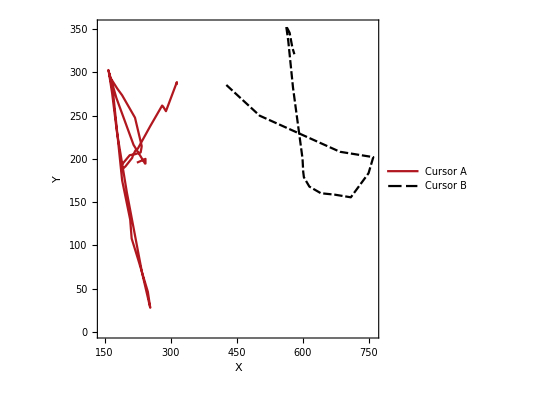
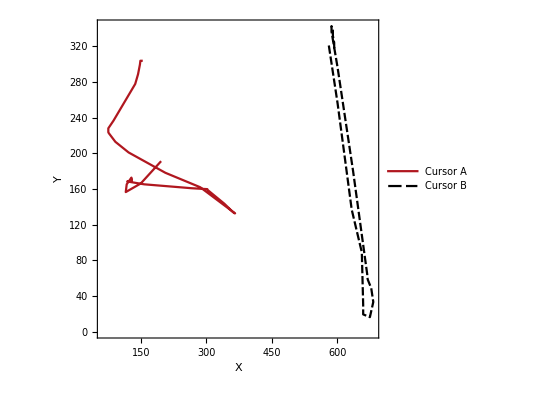
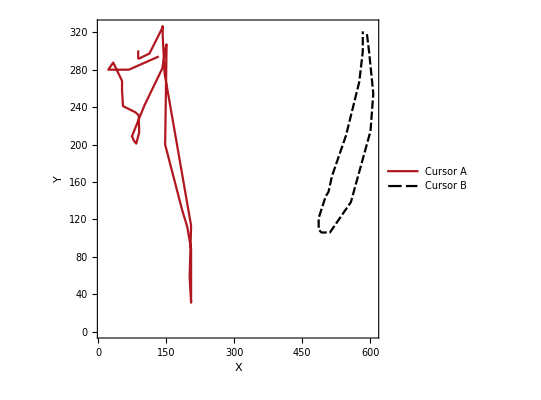

```mathematica
Table[PlotCursorPaths[1,r],{r,1,3,1}]
```

```mathematica
PositionParse[database_List]:=Map[PositionParse,Drop[database,1][[All,2]]];
GetFruitFiles[experiment_,round_,player_]:=Block[{path},
path = "Experimento_"<>ToString[experiment]<>"_Ronda_"<>ToString[round];
Select[FileNames[All,path],StringContainsQ[#,"fruit_"<>player<>"_"~~__]&]
];
GetFruitPositions[experiment_,round_,player_]:=Block[{rawData,positions},
rawData = Map[Import,GetFruitFiles[experiment,round,player]];
positions = Map[PositionParse,rawData];
Return[positions];
];
PlotFruitPositions[experiment_,round_]:=Block[{plt1,plt2},
plt1 = ListLinePlot[
GetFruitPositions[experiment,round,"PlayerA"],
FrameLabel->{Style["x",bigFontSize], Style["y",bigFontSize]}, 
ImageSize->plotSize,
PlotLabel->"PlayerA",
BaseStyle->FontSize->smallFontSize,
PlotMarkers->None,
Frame->True,
PlotRange->{{0,2000},{0,1000}}
];
plt2 = ListLinePlot[
GetFruitPositions[experiment,round,"PlayerB"],
FrameLabel->{Style["x",bigFontSize], Style["y",bigFontSize]}, 
ImageSize->plotSize,
PlotLabel->"PlayerB",
BaseStyle->FontSize->smallFontSize,
PlotMarkers->None,
Frame->True,
PlotRange->{{0,2000},{0,1000}}
];
Labeled[Row[{plt1,plt2}],"Ronda "<>ToString[round],Top]
];
```

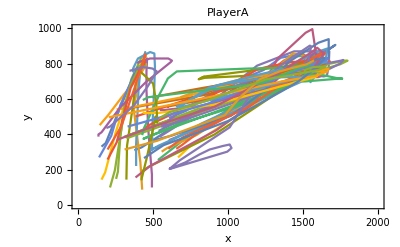
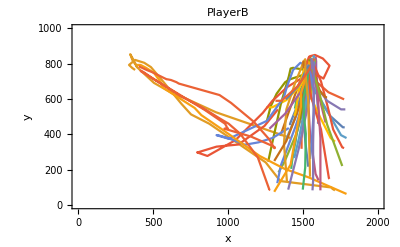
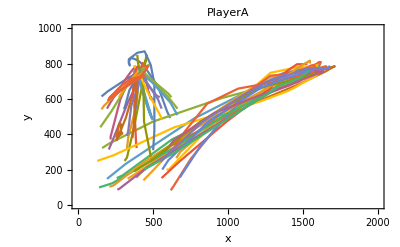
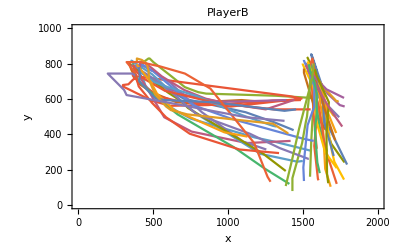
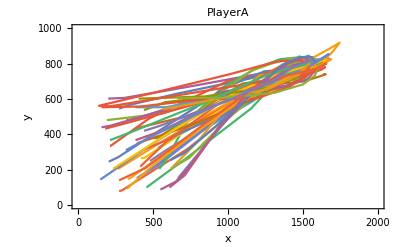
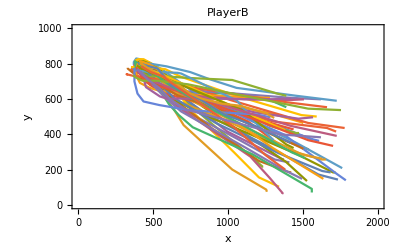
{-Graphics--Graphics-Ronda 1,-Graphics--Graphics-Ronda 2,-Graphics--Graphics-Ronda 3}

```mathematica
Table[PlotFruitPositions[1,i],{i,1,3}]
```

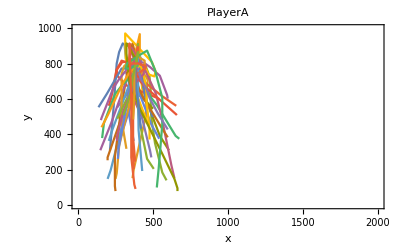
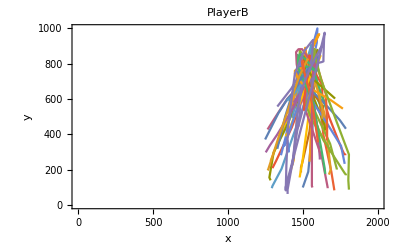
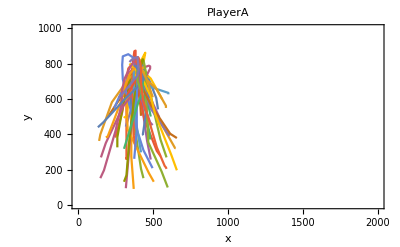
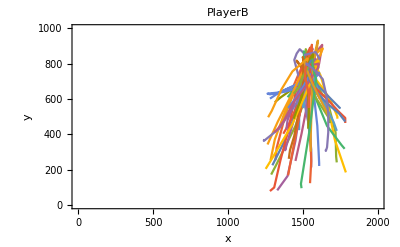
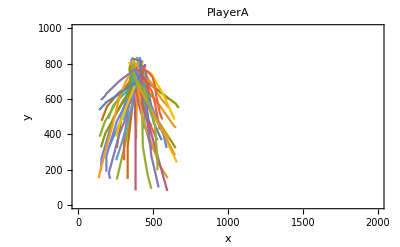
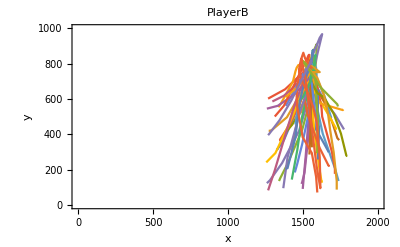
{-Graphics--Graphics-Ronda 1,-Graphics--Graphics-Ronda 2,-Graphics--Graphics-Ronda 3}

```mathematica
Table[PlotFruitPositions[6,i],{i,1,3}]
```